```mathematica
HestonPropagator[V_,τ_,λ_,θ_,ν_,ρ_,z_]:=Module[{ψp,ψm,ζ,X},
ζ=Sqrt[( λ+I z ρ ν)^2+ν^2(-I z+z^2)];
ψp=-(λ+I z ρ ν)+ζ;
ψm=( λ+I z ρ ν)+ζ;
A=-θ λ/ν^2(ψp τ+2 Log[(ψm+ψp ⅇ^(-ζ  τ))/(2 ζ)]);
B=-(-I z+z^2)(1-ⅇ^(-ζ  τ))/(ψm+ψp ⅇ^(-ζ  τ));
ⅇ^(A+B  V)]
```

```mathematica
FourierPayOffLNSepp[z_,k_]:=k^(ⅈ z+1)/(z^2-ⅈ z)
```

```mathematica
LNHestonVanillaCallIntegrand[F_,K_,z_,V_,τ_,θ_,λ_,ν_,ρ_]:=
Module[{ψp,ψm,ζ,X},
Re[ⅇ^(-Log[F] I z)HestonPropagator[V,τ,λ,θ,ν,ρ,z]FourierPayOffLNSepp[z,K]]]
```

```mathematica
LNHestonVanillaCall[F_,K_,V0_,τ_,λ_,θ_,ν_,ρ_,limsup_]:=
F-1/Pi NIntegrate[
LNHestonVanillaCallIntegrand[F,K,k1+I/2,V0,τ,θ,λ,ν,ρ],{k1,0,limsup},MaxRecursion->30]
```

```mathematica
LNHestonVanillaCallIntegrand2[F_,K_,z_,V_,τ_,θ_,λ_,ν_,ρ_]:=
Module[{},
Re[ⅇ^(-ⅈ (z)Log[F])LogNormalHestonFondamentalTransform[ρ,λ,θ,ν,V,z,τ]LogNormalCallPayOffFourierTransform[K,z]]]
```

```mathematica
HestonLogNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[ⅇ^(-ⅈ (ω +λ ⅈ)Log[S0])LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ,T]LogNormalCallPayOffFourierTransform[k,ω +λ ⅈ],
{ω,0,1000},MaxRecursion->30]]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{HestonLogNormalCallN[ρ,λv,θv,κ,V,S0,k,T],LNHestonVanillaCall[S0,k,S0,T,λv,θv,κ,ρ,1000]}]]
```

{5.125,{0.00681842,0.00761621}}

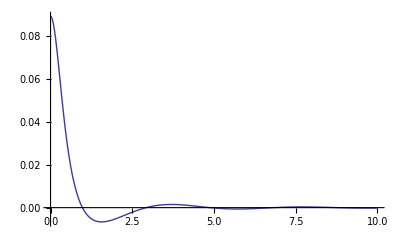

```mathematica
Module[{S=0.05,V0=0.01,τ=5,λ=0.15,θ=0.01,ν=2,ρ=-0.1,limsup=10000,K},
K=0.01;
Plot[Re[LNHestonVanillaCallIntegrand[S,K,k1+I/2,V0,τ,θ,λ,ν,ρ]],{k1,0,10},PlotRange->All]]
```

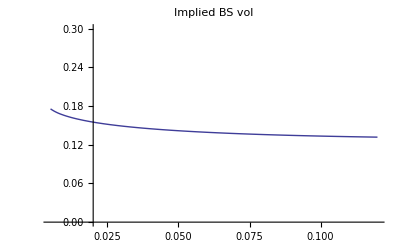
{0.969,-Graphics-}

```mathematica
Timing[Module[{S=0.05,V0=0.01,τ=5,λ=0.05,θ=0.1,ν=0.02,ρ=-0.5,limsup=10000,prices,smile,inter,coefs=LegendreCoeffs[100]},
strikes={0.005,0.0075,0.01,0.011,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};prices=Table[LNHestonVanillaCall[S,strikes[[i]],V0,τ,λ,θ,ν,ρ,limsup],{i,1,Length[strikes]}];
smile=Table[{strikes[[i]],ImpVolBS[S,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
inter=Interpolation[smile];
Plot[{inter[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",PlotRange->{0,0.3}]]]
```